```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=0
```

```mathematica
f1[t_]:=0
```

```mathematica
g0[x_]:=Sin[π x]
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→ⅇ^(-π^2 t 𝒟) Sin[π x]}}

```mathematica
Y[x,t]/.sol[[1]]
```

ⅇ^(-π^2 t 𝒟) Sin[π x]

```mathematica
Y[x,t]/.sol[[1]]/.𝒟->0.1
```

ⅇ^(-0.98696 t) Sin[π x]

```mathematica
Ya[x_,t_]:=ⅇ^(-0.9869604401089358 t) Sin[π x]
```

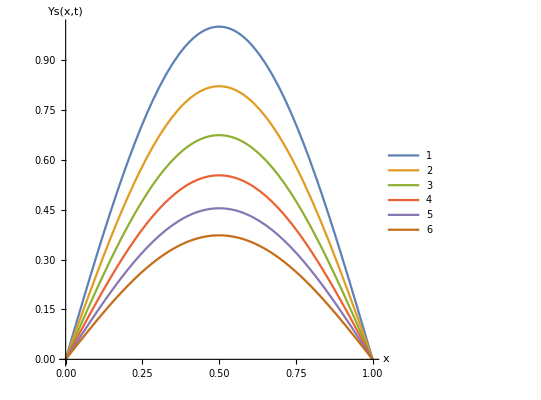

```mathematica
Plot[{Ya[x,0],Ya[x,0.2],Ya[x,0.4],Ya[x,0.6],Ya[x,0.8],Ya[x,1]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","Ys(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```

```mathematica
Ya[0.4,0.5]
```

0.580618

```mathematica
D[Ya[x,t], x]/.{x->0.4,t->0.5}
```

0.592675

```mathematica
D[Ya[x,t], t]/.{x->0.4,t->0.5}
```

-0.573047

```mathematica
D[Ya[x,t], x,x]/.{x->0.4,t->0.5}
```

-5.73047

```mathematica
D[Ya[x,t], t,t]/.{x->0.4,t->0.5}
```

0.565575

```mathematica
Sin[0.4π]
```

0.951057

```mathematica
π Cos[π x]/.x->0.4
```

0.970806

```mathematica
-π^2 Sin[π x]/.x->0.4
```

-9.38655

```mathematica
Af[x_,t_]:=(1-t)Sin[π x]
```

```mathematica
Af[x,t]/.{x->0.4,t->0.5}
```

0.475528

```mathematica
D[Af[x,t], x]/.{x->0.4,t->0.5}
```

0.485403

```mathematica
D[Af[x,t], t]/.{x->0.4,t->0.5}
```

-0.951057

```mathematica
D[Af[x,t], x,x]/.{x->0.4,t->0.5}
```

-4.69328

```mathematica
D[Af[x,t], t,t]/.{x->0.4,t->0.5}
```

0